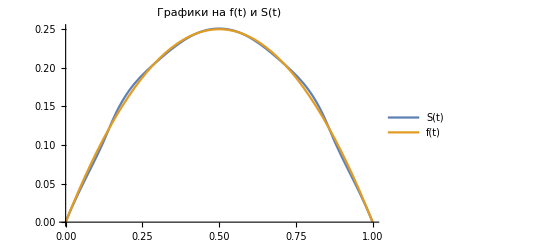

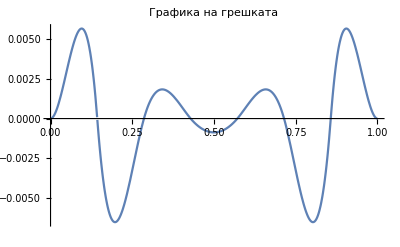

```mathematica
(*Построяване на кубичен сплайн с възли k/n на функцията f(t) = t(1-t), използван е метод на прогонката за решаване на линейна система с тридиагонална матрица*)
n=7;
f[t_]:=t*(1-t);
x[k_]:=k/n;
h[i_]:=x[i+1]-x[i];
(*инициализираме коефициентите в уравненията на системата*)
Do[a[i]=1/h[i-1],{i,1,n-1}];
Do[b[i]=2*(1/h[i-1]+1/h[i]),{i,1,n-1}];
Do[c[i]=1/h[i+1],{i,1,n-1}];
Do[d[i]=3*((f[x[i]]-f[x[i-1]])/h[i-1]^2+(f[x[i+1]]-f[x[i]])/h[i]^2),{i,1,n-1}];
(*избираме di=f'i -> т.е. полученият сплайн ще е пълна кубична интерполанта*)
m[0]=f'[x[0]];
m[n]=f'[x[n]];
(*метод на прогонката в правата посока*)
A[1]=-c[1]/b[1];
B[1]=d[1]/b[1];
Do[A[i]=(-c[i])/(a[i]*A[i-1]+b[i]); B[i]=(d[i]-a[i]*B[i-1])/(a[i]*A[i-1]+b[i]);,{i,2,n-2}];
(*метод на прогонката в обратната посока*)
m[n-1]=(d[n-1]-a[n-1]*B[n-2])/(a[n-1]*A[n-2]+b[n-1]);
For[i=n-2,i>0,i--,m[i]=A[i]*m[i+1]+B[i]];
(*след като сме намерили m[i] можем да намерим полиномите Pi[t]*)
P[i_,t_]:=f[x[i]]+m[i]*(t-x[i])+((f[x[i+1]]-f[x[i]])/h[i]-m[i])/h[i]*(t-x[i])^2+(m[i+1]-2*(f[x[i+1]]-f[x[i]])/h[i]+m[i])/h[i]^2*(t-x[i])^2*(t-x[i+1]);
(*като навържем всички полиноми Pi получаваме s(t) -> кубичен сплайн*)
sHelper[i_,t_]:=If[i<n, If[t≥x[i] && t≤x[i+1],P[i,t], sHelper[i+1,t]], 0];
S[t_]:=sHelper[0,t];
(*изчертаваме графики*)
Plot[{S[t],f[t]},{t,0,1},PlotLabel->"Графики на f(t) и S(t)", PlotLegends->{"S(t)","f(t)"}]
Plot[f[t]-S[t],{t,0,1},PlotRange->All,PlotLabel->"Графика на грешката"]
```